# Semi-Inclusive Deep Inelastic Scattering Asymptotic Term, Fixed Order Term, and Y-Term with toy models for PDFs and FFs. Based on Nadolsky, Stump, Yuan (hep-ph/9906280) (Note factor of 2 difference in Asymptotic term and 1/Q^2 difference in FO term.) - Calculate only A_1 term - Examine only quark-in-quark terms - Calculate for one flavor - Use 3-flavor alpha strong - Drop factors of A_1, σ_0, 1/(4π),1/S_eA, etc...

```mathematica
Clear["Global`*"];
```

## Basic Numerical Parameters

```mathematica
PdfType = 1;
KinematicsShow = 2;
Lambda = 0.339;   
nf = 3;
CF = 4/3;
beta0 := 11-2*nf/3;
beta1 := 102-38*nf/3;
muval = 90;(** Typical hard scale; value for Q. **)
```

## Alpha Strong

```mathematica
stdloops = 2;
alpiN[mu_,loops_] := 2/( beta0 * Log[mu/Lambda]) +
                                        If[ loops > 1, (-beta1*Log[2*Log[mu/Lambda]] / (beta0^3 * Log[mu/Lambda]^2 )), 0];
alpi[mu_] := alpiN[mu,stdloops]
```

## Toy model of quark-in-quark PDF:

```mathematica
pdf[x_,mu_]:=10.5912(x^(.8 - .07 Log[mu/.2])) (1 - x)^1.1
```

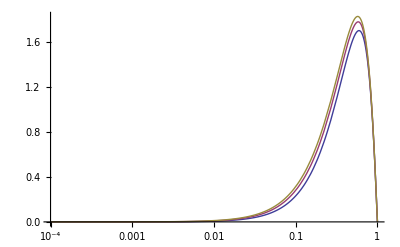

```mathematica
LogLinearPlot[{x pdf[x,3],x pdf[x,10],x pdf[x,20]},{x,.0001,1}]
```

```mathematica
1/ Integrate[x pdf[x,2],{x,0,1}]
```

1.

## CTEQ 10 PDFs:

```mathematica
(*here=Directory[];*)
here="/Users/tedrogers/Dropbox/TedBenwork/sidis"(*DBC--SET THIS LINE TO THE LOCATION OF YOUR /Dropbox/TedBenwork/sidis FOLDER*)
pdfPackLoc=StringDrop[here,-5]<>"MMA_pac/";(*the directory containing the parsing package is in the Dropbox folder, one level up, in a folder called MMA_pac*)
SetDirectory[pdfPackLoc];
<<pdfParse.m;
SetDirectory[here];
pdfParseCTEQ["ct10.00.pds"]
```

/Users/tedrogers/Dropbox/TedBenwork/sidis

- Required Package: pdfCalc --Loaded -

===============================================================

- pdfParse -

Version:  1.0

Authors: D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of avialable commands, enter: ?pdf*

===============================================================

PDF Table for Fit #: cx22a

1

```mathematica
If[PdfType ==1,
Clear[pdf];
pdf[x_,mu_]:=pdfFunction[1,1,x,mu];(*central value ct10 pdf.flavor=1 coresponds to UP QUARK pdf function is pdfFunction[setNumber,flavorNuber,x,Q]*),
pdf[x,mu]]
```

10.5912 (1-x)^1.1 x^(0.8-0.07 Log[5. mu])

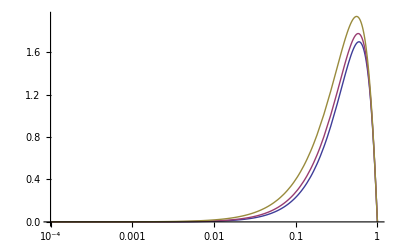

```mathematica
LogLinearPlot[{x pdf[x,3],x pdf[x,10],x pdf[x,90]},{x,.0001,1}]
```

```mathematica
pdf[.1,2]
```

2.16667

#### The momentum fraction for the up quark at 2 GeV.

```mathematica
NIntegrate[ x pdf[x,2],{x,0,1}]
```

0.999996

#### Total momentum for all flavors.

```mathematica
Off[NIntegrate::izero];
Off[NIntegrate::ncvb];
Sum[NIntegrate[ x pdfFunction[1,i,x,2],{x,pdfXmin[1],1}],{i,-5,5}]
```

0.999695

## Toy model of quark-in-quark fragmentation function

```mathematica
frag[z_,mu_] :=5.5546(z^(.04- .01 Log[mu/.1])) (1 - z)^.9
```

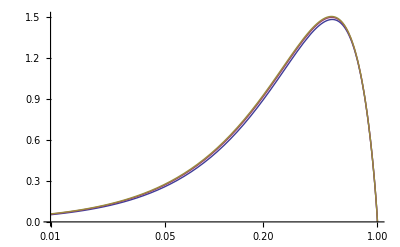

```mathematica
LogLinearPlot[{z frag[z,2],z frag[z,10],z frag[z,20]},{z,.01,1}]
```

```mathematica
1/ Integrate[z frag[z,2],{z,0,1}]
```

1.

## The fixed order term (FO): Ref.[1] Eq.(85,89) and Eq.(B2). - ξ_a , ξ_b: Longitudal + and - momentum fraction for the PDF and FF respectively. - x: Bjorken x. - z: Standard SIDIS z. - xhat: x/ξ_a , Eq.(25). - zhat: z/ξ_b , Eq.(26). - z(x)hatFixed: The value of zhat at the delta function of Eq.(B7), in terms of ξ_a (ξ_b). - doubleu, w: Eq.(88).

```mathematica
xhat[x_,xia_]:= x / xia; (** Definition of x̂, Eq.(25) **)
zhat[z_,xib_]:= z / xib; (** Definition of ẑ, Eq.(26) **)
zhat1[xh_,qt_,Q_]:= (1 - xh) / (((qt^2/Q^2) - 1)xh + 1) (** Value of ẑ fixed by δ function, Eq.(B7), 
here written in terms of an arbitrary xh. **)
xhat1[zh_,qt_,Q_]:= (1 - zh) / (((qt^2/Q^2) - 1)zh + 1) (** Analogous for x̂. **)
```

```mathematica
zhatFixed[z_,xia_,qt_,Q_] := zhat1[xhat[z,xia],qt,Q]  (** Eq.(B7) at the delta function value of x̂. **)
xhatFixed[x_,xib_,qt_,Q_] := xhat1[zhat[x,xib],qt,Q]  (** Analogous for ẑ. **)
```

```mathematica
xiamin[w_,x_,z_]:=w^2 /(1 - z) + x   (** Eq.(86) **) 
xibmin[w_,x_,z_]:=w^2 /(1 - x) + z   (** Eq.(87) **)
```

```mathematica
doubleu[x_, z_, qt_, Q_] := (qt/Q) Sqrt[x z] (** Eq.(88) **)
```

```mathematica
Clear[xiaval];
xiaval[x_,z_,qt_,Q_,xib_] := x((qt^2/Q^2) + (xib/z - 1))/(xib/z -1) (** Subscript[ξ, a] in terms of Subscript[ξ, b] at the  δ-function. **)
Clear[xibval];
xibval[x_,z_,qt_,Q_,xia_] := z((qt^2/Q^2) + (xia/x - 1))/(xia/x -1) (** Subscript[ξ, b] in terms of Subscript[ξ, a] at the  δ-function. **)
```

```mathematica
Intersectxib[x_,z_,xib_]:= xib + (x - z) (** Line of slope 1 and intersecting (Subscript[ξ, a] = x, Subscript[ξ, b]= z) . **)
```

## Visualize Kinematics

```mathematica
zvalue = 0.6; (** Fix the kinematical variables at some sample values. **)
xvalue = 0.1;
qtvalue = (1/2)muval;
```

```mathematica
(** Define some lines. **)
line1=Line[{{xibmin[doubleu[xvalue,zvalue,qtvalue,muval],xvalue,zvalue],0},{xibmin[doubleu[xvalue,zvalue,qtvalue,muval],xvalue,zvalue],1.2}}];
(** Line indicating the position of the kinemaical minimum of Subscript[ξ, b]. **)
line2=Line[{{0,xiamin[doubleu[xvalue,zvalue,qtvalue,muval],xvalue,zvalue]},{1.2,xiamin[doubleu[xvalue,zvalue,qtvalue,muval],xvalue,zvalue]}}];
(** Line indicating the position of the kinemaical minimum of Subscript[ξ, a]. **)
```

```mathematica
smallqtPlot =Plot[{xiaval[xvalue,zvalue,muval/100,muval,xib]},{xib,zvalue,1.2},PlotRange->{{0,1.2},{0,1.2}},Epilog->{Directive[Thick],line1,line2}]; (** Kinematical Contour for small Subscript[q, T] , and line at z. **)
xyPlot =Plot[{Intersectxib[xvalue,zvalue,xib]},{xib,0.0,1.2},PlotStyle->{Dashed,Black},PlotRange->{{0,1.2},{0,1.2}}]; (** Line of slope 1 and intersecting (Subscript[ξ, a] = x, Subscript[ξ, b]= z) . **)
fullPlot =Plot[{xiaval[xvalue,zvalue,qtvalue,muval,xib]},{xib,xibmin[doubleu[xvalue,zvalue,qtvalue,muval],xvalue,zvalue],1},PlotRange->{{0,1.2},{0,1.2}},PlotStyle->{Red,Thick}]; (** Plot of full contour for integral in Eq.(84). **)
xbranchPlot = Plot[{xiaval[xvalue,zvalue,qtvalue,muval,xib]HeavisideTheta[1 - xib]HeavisideTheta[1 - xiaval[xvalue,zvalue,qtvalue,muval,xib]]},{xib,zvalue + doubleu[xvalue,zvalue,qtvalue,muval],1},PlotRange->{{0,1.2},{0,1.2}},PlotStyle->{Red,Thick}]; (** Plot of the branch for integral for the first term in Eq.(89). **)
zbranchPlot = Plot[{xiaval[xvalue,zvalue,qtvalue,muval,xib]HeavisideTheta[1 - xib]HeavisideTheta[1 - xiaval[xvalue,zvalue,qtvalue,muval,xib]]},{xib,xibmin[doubleu[xvalue,zvalue,qtvalue,muval],xvalue,zvalue],zvalue + doubleu[xvalue,zvalue,qtvalue,muval]},PlotRange->{{0,1.2},{0,1.2}},PlotStyle->{Green,Thick}]; (** Plot of the branch for integral for the second term in Eq.(89). **)
```

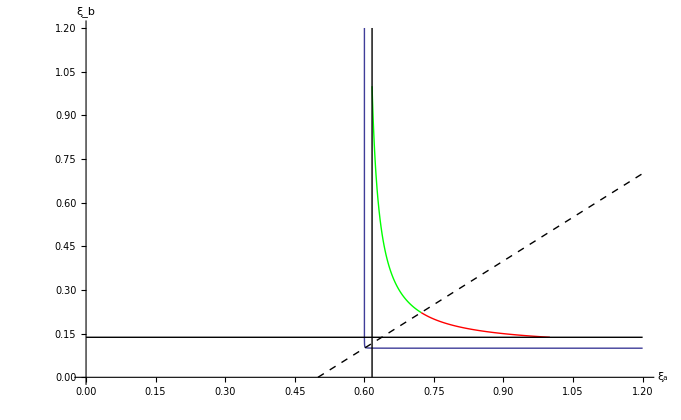

```mathematica
Show[{smallqtPlot,xbranchPlot,zbranchPlot,xyPlot},AxesLabel->{Subscript[ξ, a],Subscript[ξ, b]}] (** Compare with Figure 6 of Nadolsky, Stump, Yuan. **)
```

```mathematica
Clear[line1p]; Clear[line2p]; Clear[line3]; Clear[line4];line1p[qtv_,xv_,zv_]:=Line[{{xibmin[doubleu[xv,zv,qtv,muval],xv,zv],0},{xibmin[doubleu[xv,zv,qtv,muval],xv,zv],1.2}}];
line2p[qtv_,xv_,zv_]:=Line[{{0,xiamin[doubleu[xv,zv,qtv,muval],xv,zv]},{1.2,xiamin[doubleu[xv,zv,qtv,muval],xv,zv]}}];
line3[zv_]:=Line[{{zv,0},{zv,1.2}}];
line4[xv_]:=Line[{{0,xv},{1.2,xv}}];
line5[xv_]:=Line[{{0,1},{1.2,1.0}}];
line6[xv_]:=Line[{{1,0},{1.0,1.2}}];
```

```mathematica
If[KinematicsShow == 1,
Clear[AA];
AA[qtv_,xv_,zv_] :=Plot[{xiaval[xv,zv,qtv,muval,xib]HeavisideTheta[1 - xib]HeavisideTheta[1 - xiaval[xv,zv,qtv,muval,xib]],Intersectxib[xv,zv,xib]},{xib,zv,1.2},PlotStyle->{{Thick,Blue},{Red}},PlotRange->{{0.0,1.2},{0.001,1.2}},AxesLabel->{Subscript[ξ, a],Subscript[ξ, b]},Epilog->{Directive[Thick],line1p[qtv,xv,zv],Directive[Thick],line2p[qtv,xv,zv],Directive[Dashed],line3[zv],line4[xv],Directive[Black,Dotted],line5[xv],line6[xv]}];
KinAni = Manipulate[AA[qtv,xv,zv],{{qtv,muval/3,"q_T"},muval/100,muval},{{xv,0.1,"Bjorken x"},.01,.2},{{zv,zvalue,"z"},.4,.85}](** Compare with Figure 6 of Nadolsky, Stump, Yuan. **),
Print["No Animation"]]
```

## Return to calculation of fixed order term:

### Unpolarized factor in Eq.(B2); Lower case f but without the A_1

```mathematica
Clear[Coeffa];
Coeffa[Q_,qt_,xia_,x_,mu_]:= 2 CF alpi[mu]xhat[x,xia] zhatFixed[x,xia,qt,Q]((1/(qt^2)) ((Q^4/(xhat[x,xia]^2 zhatFixed[x,xia,qt,Q]^2)) + (Q^2 - qt^2)^2) + 6 Q^2)
```

```mathematica
Coeffb[Q_,qt_,xib_,z_,mu_]:= 2 CF alpi[mu]zhat[z,xib] xhatFixed[z,xib,qt,Q]((1/(qt^2)) ((Q^4/(xhatFixed[z,xib,qt,Q]^2 zhat[z,xib]^2)) + (Q^2 - qt^2)^2) + 6 Q^2)
```

### Integrands in the two branches: the first and second terms in Eq.(83), using the integrations over ξ_a and ξ_b respectively.

```mathematica
Mbranch1[Q_,qt_,z_,xia_,x_,mu_]:= Re[ (xhat[x,xia] zhatFixed[x,xia,qt,Q]/(xia - x))Coeffa[Q,qt,xia,x,mu]pdf[xia,mu]frag[z/zhatFixed[x,xia,qt,Q],mu]/Q^4]
```

```mathematica
Mbranch2[Q_,qt_,z_,xib_,x_,mu_]:= Re[ (zhat[z,xib] xhatFixed[z,xib,qt,Q]/(xib - z))Coeffb[Q,qt,xib,z,mu]pdf[x/xhatFixed[z,xib,qt,Q],mu]frag[xib,mu] /Q^4]
```

### Evalution of Integrals in Eq.(83). Note the integration limits:

```mathematica
FixedOrder2[Q_,qt_,z_,x_] := NIntegrate[Mbranch1[Q,qt,z,xia,x,Q],{xia,x + doubleu[x, z, qt, Q],1}]+NIntegrate[Mbranch2[Q,qt,z,xib,x,Q],{xib,z + doubleu[x, z, qt, Q],1}]
```

## The Asymptotic term (ASY): Eq.(36) in Ref.[1].

### Define the Plus Distribution in Eq.(39,40):

```mathematica
SetAttributes[{PlusDist,pdfconvo,ffconvo},HoldAll];
```

```mathematica
PlusDist[minval_,f_[xmin_,x_,mu_]]:= NIntegrate[((1 + x^2) f[xmin,x,mu]/x- (2) f[xmin,1,mu])/(1-x),{x,minval+.0001,1}] + 2 f[xmin,1,mu]Log[1 - minval] +(3/2) f[xmin,1,mu]
```

### The PDF and Fragmentation Function in a form for convolution with the + distribution:

```mathematica
pdfconvo[x_,xi_,mu_]:=pdf[x/xi,mu]
ffconvo[z_,xi_,mu_]:= frag[z/xi,mu]
```

### The quark-to-quark terms in Eq.(36):

```mathematica
(** First Term in Eq.(40). **)
AsyTerm1[z_,ex_,mu_]:= CF frag[z,mu] PlusDist[ex,pdfconvo[ex,xi,mu]]
```

```mathematica
(** Third Term in Eq.(40). **)
AsyTerm3[z_,x_,mu_]:= CF pdf[x,mu] PlusDist[z,ffconvo[z,xi,mu]]
```

```mathematica
(** Fifth Term in Eq.(40). **)
AsyTerm5[z_,x_,mu_,qt_] := 2 pdf[x,mu] frag[z,mu] (CF( Log[mu^2/qt^2] - (3/2)))
```

### Complete Asymptotic part (with alpha strong and 1/q_T^2)

```mathematica
Asymptot[z_,ex_,mu_,qt_]:=2(alpi[mu]/(qt^2))(AsyTerm1[z,ex,mu] + AsyTerm3[z,ex,mu] + AsyTerm5[z,ex,mu,qt])
```

## Plot of Both Fixed Order and Asymptotic Parts:

```mathematica
AsymptPlot = LogPlot[{Abs[Asymptot[zvalue,xvalue,muval,qt]]},{qt,muval/1000,muval},PlotRange-> {.00001,1.2},PlotStyle->{Thick,Red,Dashed}];
```

```mathematica
(*DBC--THERE IS AN ERROR HERE IN CREATING THE Y-TERM TABLE. LOOK AT EACH TERM INTEPENDENTLY WITH MULTIPLE PDF FUNCTIONS.*)
```

```mathematica
Clear[tableYterm];
tableYterm = {};
Do[tableYterm=Append[tableYterm ,{i muval/1000,-Asymptot[zvalue,xvalue,muval,i muval/1000]+FixedOrder2[muval,i muval/1000,zvalue,xvalue]}](*;
If[Length[$MessageList]≠0,
Print["Integration Error generated at iteration #", i];
Unprotect[$MessageList];
    Do[$MessageList={},{1}];
    Protect[$MessageList]
]*),(*End If...*)(*DBC--added to find terms that do not integrate properly.*)
{i,1000}]
```

```mathematica
YtermForPlot =Interpolation[tableYterm];
```

```mathematica
YtermPlot = LogPlot[YtermForPlot[qt],{qt,muval/1000,muval},PlotRange-> {.00001,1.2},PlotStyle->{Purple,Thick}];
```

```mathematica
Clear[tableFixedOrder];
tableFixedOrder = {};
Do[tableFixedOrder=Append[tableFixedOrder,{i muval/1000,FixedOrder2[muval,i muval/1000,zvalue,xvalue]}](*;If[Length[$MessageList]≠0,
Print["Integration Error generated at iteration #", i];
Unprotect[$MessageList];
    Do[$MessageList={},{1}];
    Protect[$MessageList]
]*),(*End If...*)(*DBC--added to find terms that do not integrate properly.*)
{i,1000}]
```

```mathematica
FixedOrderForPlot =Interpolation[tableFixedOrder];
```

```mathematica
FixedOrderPlot = LogPlot[FixedOrderForPlot[qt],{qt,muval/1000,muval},PlotRange-> {.00001,1.2},PlotStyle->{Blue,Thick,Dashed}];
```

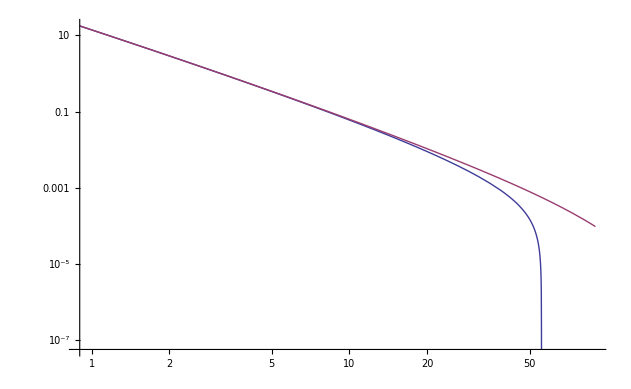

```mathematica
LogLogPlot[{Asymptot[zvalue,xvalue,muval,qt],FixedOrderForPlot[qt]},{qt,muval/100 ,muval}]
```

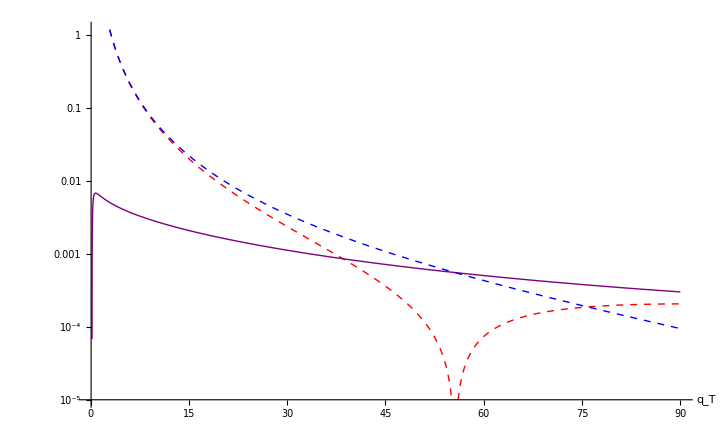

```mathematica
Show[{AsymptPlot,YtermPlot,FixedOrderPlot},AxesLabel->{Subscript[q, T], ""}]
```

#### Estimate the error in dropping the Y-term by plotting the ratio of the asymptotic term to fixed order term.

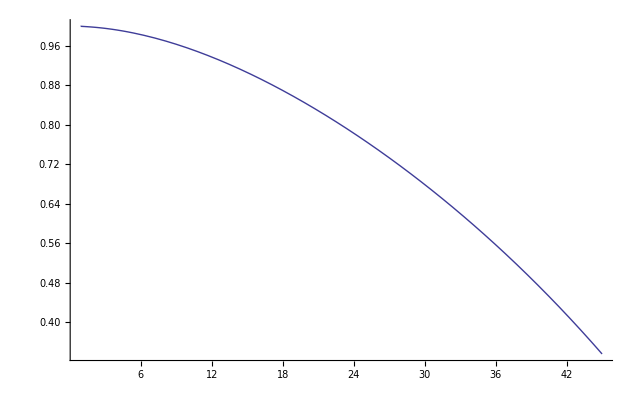

```mathematica
Plot[{Asymptot[zvalue,xvalue,muval,qt]/FixedOrderForPlot[qt]},{qt,muval/100,muval/2}]
```

#### DBC--looking at induvidual terms to find the offensive one.

```mathematica
tableYterm[[178;;182]]
```

{{801/50,0.00199725},{1611/100,0.0019884},{81/5,0.00197961},{1629/100,0.00197089},{819/50,0.00196224}}

```mathematica
tableFixedOrder[[178;;182]]
```

{{801/50,0.0188736},{1611/100,0.0186016},{81/5,0.0183348},{1629/100,0.0180732},{819/50,0.0178166}}

```mathematica
Asymptot[zvalue, xvalue, muval, 1629/100]
```

0.0161023